## Kernels

```mathematica
LaunchKernels[]
```

```mathematica
Needs["SubKernels`RemoteKernels`"]
```

```mathematica
LaunchKernels[RemoteMachine["server",7]]
```

{KernelObject[17,node01],KernelObject[18,node01],KernelObject[19,node01],KernelObject[20,node01],KernelObject[21,node01],KernelObject[22,node01],KernelObject[23,node01],KernelObject[24,node01]}

```mathematica
LaunchKernels[RemoteMachine["node02",8]]
```

{KernelObject[25,node02],KernelObject[26,node02],KernelObject[27,node02],KernelObject[28,node02],KernelObject[29,node02],KernelObject[30,node02],KernelObject[31,node02],KernelObject[32,node02]}

```mathematica
LaunchKernels[RemoteMachine["node03",8]]
```

{KernelObject[33,node03],KernelObject[34,node03],KernelObject[35,node03],KernelObject[36,node03],KernelObject[37,node03],KernelObject[38,node03],KernelObject[39,node03],KernelObject[40,node03]}

```mathematica
LaunchKernels[RemoteMachine["node04",8]]
```

{KernelObject[41,node04],KernelObject[42,node04],KernelObject[43,node04],KernelObject[44,node04],KernelObject[45,node04],KernelObject[46,node04],KernelObject[47,node04],KernelObject[48,node04]}

## Constants

```mathematica
(*SetDirectory["/Users/shainen/Dropbox/Research/bhsucon/nb/nb"];*)
```

```mathematica
SetDirectory["/Users/shainen/Dropbox/Research/bhsucon/nb/nb"];
```

```mathematica
Get["constants.m"]
```

```mathematica
su2Runs=100
```

100

## Dynamic Equations

```mathematica
vs=Table[Table[s[m,n][t],{n,1,3}],{m,1,Sites}];
vscor=Table[Table[s[m,n][t]s[l,n][t],{n,1,3}],{m,1,Sites},{l,1,Sites}];
ds=Table[Table[s[m,n]'[t],{n,1,3}],{m,1,Sites}];
initialss=Flatten[Table[Table[s[m,n][0]==Subscript[s, 0][m,n],{n,1,3}],{m,1,Sites}]];
Δs[m_,ow_]:=Table[D[ow,s[m,n][t]],{n,1,3}];
```

```mathematica
sw[m_,ow_]:=vs[[m]]  ow-ⅈ/2 vs[[m]] ×Δs[m,ow]-1/8(Δs[m,ow]+Table[vs[[m]] .Δs[m,Δs[m,ow][[n]]],{n,1,3}]-1/2 vs[[m]]  Sum[Δs[m,Δs[m,ow][[n]]][[n]],{n,1,3}]);
swb[m_,ow_]:=vs[[m]]  ow+ⅈ/2 vs[[m]] ×Δs[m,ow]-1/8(Δs[m,ow]+Table[vs[[m]] .Δs[m,Δs[m,ow][[n]]],{n,1,3}]-1/2 vs[[m]]  Sum[Δs[m,Δs[m,ow][[n]]][[n]],{n,1,3}]);
```

```mathematica
Hs[m_,ow_]:=U/2 sw[m,sw[m,ow][[3]]][[3]]-J navg (sw[m,ow][[1]](Sum[sw[n,1][[1]],{n,1,m-1}]+Sum[sw[n,1][[1]],{n,m+1,Sites}])+sw[m,ow][[2]](Sum[sw[n,1][[2]],{n,1,m-1}]+Sum[sw[n,1][[2]],{n,m+1,Sites}]))-μ sw[m,ow][[3]];
Hsb[m_,ow_]:=U/2 swb[m,swb[m,ow][[3]]][[3]]-J navg (swb[m,ow][[1]](Sum[swb[n,1][[1]],{n,1,m-1}]+Sum[swb[n,1][[1]],{n,m+1,Sites}])+swb[m,ow][[2]](Sum[swb[n,1][[2]],{n,1,m-1}]+Sum[swb[n,1][[2]],{n,m+1,Sites}]))-μ swb[m,ow][[3]];
```

```mathematica
eqnss1=Table[ds[[1,n]]==Simplify[ⅈ (Hs[1,vs[[1,n]]]-Hsb[1,vs[[1,n]]])],{n,1,3}]
```

{s[1,1]'[t]==s[1,2][t] (μ-U s[1,3][t])-J navg s[1,3][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]),s[1,2]'[t]==s[1,1][t] (-μ+U s[1,3][t])+J navg s[1,3][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t]),s[1,3]'[t]==J navg (-s[1,2][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[1,1][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))}

```mathematica
eqnss=Flatten[Table[eqnss1/.Flatten[Table[{s[1,n]'[t]->s[m,n]'[t],s[1,n][t]->s[m,n][t],s[m,n][t]->s[1,n][t]},{n,1,3}]],{m,1,Sites}]];
```

```mathematica
MatrixForm[eqnss]
```

(s[1,1]'[t]==s[1,2][t] (μ-U s[1,3][t])-J navg s[1,3][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])
s[1,2]'[t]==s[1,1][t] (-μ+U s[1,3][t])+J navg s[1,3][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])
s[1,3]'[t]==J navg (-s[1,2][t] (s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[1,1][t] (s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))
s[2,1]'[t]==s[2,2][t] (μ-U s[2,3][t])-J navg s[2,3][t] (s[1,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])
s[2,2]'[t]==s[2,1][t] (-μ+U s[2,3][t])+J navg s[2,3][t] (s[1,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])
s[2,3]'[t]==J navg (-s[2,2][t] (s[1,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[2,1][t] (s[1,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))
s[3,1]'[t]==s[3,2][t] (μ-U s[3,3][t])-J navg s[3,3][t] (s[1,2][t]+s[2,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t])
s[3,2]'[t]==s[3,1][t] (-μ+U s[3,3][t])+J navg s[3,3][t] (s[1,1][t]+s[2,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])
s[3,3]'[t]==J navg (-s[3,2][t] (s[1,1][t]+s[2,1][t]+s[4,1][t]+s[5,1][t]+s[6,1][t])+s[3,1][t] (s[1,2][t]+s[2,2][t]+s[4,2][t]+s[5,2][t]+s[6,2][t]))
s[4,1]'[t]==s[4,2][t] (μ-U s[4,3][t])-J navg s[4,3][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[5,2][t]+s[6,2][t])
s[4,2]'[t]==s[4,1][t] (-μ+U s[4,3][t])+J navg s[4,3][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[5,1][t]+s[6,1][t])
s[4,3]'[t]==J navg (-s[4,2][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[5,1][t]+s[6,1][t])+s[4,1][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[5,2][t]+s[6,2][t]))
s[5,1]'[t]==s[5,2][t] (μ-U s[5,3][t])-J navg s[5,3][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[6,2][t])
s[5,2]'[t]==s[5,1][t] (-μ+U s[5,3][t])+J navg s[5,3][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[6,1][t])
s[5,3]'[t]==J navg (-s[5,2][t] (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[6,1][t])+s[5,1][t] (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[6,2][t]))
s[6,1]'[t]==-J navg (s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]) s[6,3][t]+s[6,2][t] (μ-U s[6,3][t])
s[6,2]'[t]==J navg (s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]) s[6,3][t]+s[6,1][t] (-μ+U s[6,3][t])
s[6,3]'[t]==J navg ((s[1,2][t]+s[2,2][t]+s[3,2][t]+s[4,2][t]+s[5,2][t]) s[6,1][t]-(s[1,1][t]+s[2,1][t]+s[3,1][t]+s[4,1][t]+s[5,1][t]) s[6,2][t]))

## Wigner with neg prob

```mathematica
svarsingreek={1/2 (β Conjugate[α]+α Conjugate[β]),1/2 (-ⅈ β Conjugate[α]+ⅈ α Conjugate[β]),1/2 (α Conjugate[α]-β Conjugate[β])};
```

```mathematica
Norm1=(4-√ⅇ)/(√ⅇ);
```

```mathematica
Norm2=ⅇ^(-1-1/(√2)) (4 (2+√2)+4 (-2+√2) ⅇ^(√2)+ⅇ^(1+1/(√2)));
```

```mathematica
Fock1Mag=ProbabilityDistribution[4 a ⅇ^(-2 a^2)Abs[(4 a^2-1)]/Norm1,{a,0,∞}];
```

```mathematica
Fock2Mag=ProbabilityDistribution[4 a ⅇ^(-2 a^2)Abs[(1-8 a^2+8 a^4)]/Norm2,{a,0,∞}];
```

```mathematica
randmag1=RandomVariate[Fock1Mag,{2,Sites,su2Runs}];
```

```mathematica
randmag2=RandomVariate[Fock2Mag,{Sites,su2Runs}];
```

```mathematica
metric1=1-2UnitStep[1/2-randmag1];
```

```mathematica
metric2=1-2UnitStep[randmag2-(√(2-√2))/2]*UnitStep[(√(2+√2))/2-randmag2];
```

```mathematica
randphase=RandomReal[{0,2π},{2,Sites,su2Runs}];
```

```mathematica
randrest=Table[RandomVariate[NormalDistribution[0,1/2]]+I RandomVariate[NormalDistribution[0,1/2]],{Sites},{su2Runs}];
```

```mathematica
randupinit[n_]:={randmag2[[n]] ⅇ^(ⅈ randphase[[1,n]]),randrest[[n]]};
randmiinit[n_]:={randmag1[[1,n]] ⅇ^(ⅈ randphase[[1,n]]),randmag1[[2,n]] ⅇ^(ⅈ randphase[[2,n]])};
randdoinit[n_]:={randrest[[n]],randmag2[[n]] ⅇ^(ⅈ randphase[[1,n]])};
```

```mathematica
(*randinits={randupinit[1],randmiinit[2],randdoinit[3],randupinit[4],randmiinit[5],randdoinit[6]};*)
```

```mathematica
randinits=Table[randupinit[n],{n,1,updownmiddle[[1]]}]~Join~Table[randdoinit[n],{n,updownmiddle[[1]]+1,updownmiddle[[1]]+updownmiddle[[2]]}]~Join~Table[randmiinit[n],{n,updownmiddle[[1]]+updownmiddle[[2]]+1,updownmiddle[[1]]+updownmiddle[[2]]+updownmiddle[[3]]}];
```

```mathematica
ResNorm=Norm2^(updownmiddle[[1]]+updownmiddle[[2]])Norm1^(2updownmiddle[[3]]);
```

```mathematica
ProgressIndicator[Dynamic[su2Runsdone],{0,su2Runs}]
```

```mathematica
spindyn=Table[0,{Nt},{1},{Sites},{3}];
spincordyn=Table[0,{Nt},{1},{Sites},{Sites},{3}];
SetSharedVariable[spindyn];
SetSharedVariable[spincordyn];
su2Runsdone=0;
SetSharedVariable[su2Runsdone];
Timing[
ParallelDo[
sol=NDSolve[(eqnss~Join~initialss)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[s, 0][m,n]->(svarsingreek[[n]]/.{α->randinits[[m,1,j]],β->randinits[[m,2,j]]}),{m,1,Sites},{n,1,3}]],Flatten[vs],{t,0,tmax},MaxSteps->∞
];
metprod=Product[metric1[[n,m,j]],{n,1,2},{m,updownmiddle[[1]]+updownmiddle[[2]]+1,updownmiddle[[1]]+updownmiddle[[2]]+updownmiddle[[3]]}]Product[metric2[[m,j]],{m,1,updownmiddle[[1]]+updownmiddle[[2]]}];
TWAresspin=metprod vs/.sol;
TWArescor=metprod vscor/.sol;
spindyn+=Table[TWAresspin,{t,ts}];
spincordyn+=Table[TWArescor,{t,ts}];
su2Runsdone++;
,{j,1,su2Runs}
]
]
avgspins2=ResNorm Re[spindyn[[All,1]]]/su2Runs;
avgcor2=ResNorm Re[spincordyn[[All,1]]]/su2Runs;
```

{5.39278,Null}

```mathematica
(*Save["sp"<>su2outfile,avgspins2]*)
```

```mathematica
(*Save["cor"<>su2outfile,avgcor2]*)
```

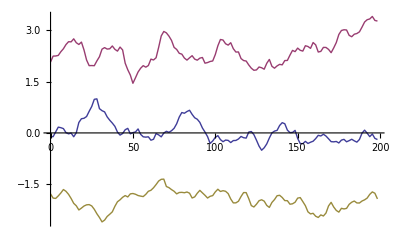

```mathematica
ListPlot[Table[{times,avgspins2[[All,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotRange->All]
```

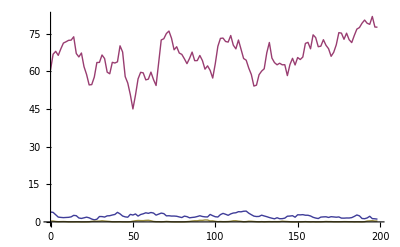

```mathematica
ListPlot[Table[{times,avgcor2[[All,n,n,3]]^2}ᵀ,{n,1,3}],Joined->True,PlotRange->All]
```